```mathematica
(* Note that this code works in dimensionless variables A(ρ), F(ρ), P(ρ) *)
(* These are related to the variables in the companion paper via ρ = r√(3Subscript[λM, P]^2/8π), A = R√(3Subscript[λM, P]^2/8π), F = f√(8π/3 Subscript[M, P]^2), P = ϕ√(8π/3 Subscript[M, P]^2) *)
ClearAll["Global'*"];
SetDirectory[NotebookDirectory[]];
<<dilaton.m; (* Import package dilaton.m *)
λ = 0.1; (* Choose quartic coupling *)
ϕ0[g_]:= 0.643 + Log[g]/√3; (* Empirical fit between string coupling Subscript[g, s] and initial condition ϕ(0) *)
```

Successfully loaded dilaton.m

```mathematica
{g, fa }= {0.2, 10^17 GeV}; (* Set string coupling and decay constant *)
```

```mathematica
IterateSolver[ϕ0[g], λ, fa, 40]; (* Find the correct initial condition for F(0) and solve for the dynamics *)
(* Note that this may take a while. If Subscript[ρ, max] > O(1000), then you can safely abort the loop and plot the results *)
```

Run 1: F(0) = 1.75, ρ_max = 0.10211

F'(ρ_max) = -0.705581, A'(ρ_max) = 0.98862

Run 2: F(0) = 2.375, ρ_max = 1.9080

F'(ρ_max) = 82.3192, A'(ρ_max) = 0.99411

Run 3: F(0) = 2.0625, ρ_max = 0.35422

F'(ρ_max) = -2.73837, A'(ρ_max) = 0.99979

Run 4: F(0) = 2.21875, ρ_max = 3.2017

F'(ρ_max) = 461.868, A'(ρ_max) = 0.99766

Run 5: F(0) = 2.140625, ρ_max = 5.8900

F'(ρ_max) = 456.919, A'(ρ_max) = 0.99925

Run 6: F(0) = 2.101563, ρ_max = 52.885

F'(ρ_max) = 466.621, A'(ρ_max) = 0.99999

Run 7: F(0) = 2.082031, ρ_max = 0.51266

F'(ρ_max) = -1.39077, A'(ρ_max) = 0.99992

Run 8: F(0) = 2.091797, ρ_max = 0.74336

F'(ρ_max) = -0.688565, A'(ρ_max) = 0.99997

Run 9: F(0) = 2.09668, ρ_max = 1.0921

F'(ρ_max) = -0.327741, A'(ρ_max) = 0.99999

Run 10: F(0) = 2.099121, ρ_max = 1.6665

F'(ρ_max) = -0.143463, A'(ρ_max) = 0.99999

Run 11: F(0) = 2.100342, ρ_max = 2.8590

F'(ρ_max) = -0.0494643, A'(ρ_max) = 1.

Run 12: F(0) = 2.100952, ρ_max = 18.519

F'(ρ_max) = -0.0012073, A'(ρ_max) = 1.

Run 13: F(0) = 2.101257, ρ_max = 80.525

F'(ρ_max) = 590.822, A'(ρ_max) = 1.

Run 14: F(0) = 2.101105, ρ_max = 145.95

F'(ρ_max) = 451.335, A'(ρ_max) = 1.

Run 15: F(0) = 2.101028, ρ_max = 185.13

F'(ρ_max) = -0.0000630276, A'(ρ_max) = 1.

Run 16: F(0) = 2.101067, ρ_max = 248.29

F'(ρ_max) = -0.0000157101, A'(ρ_max) = 1.

Run 17: F(0) = 2.101086, ρ_max = 181.53

F'(ρ_max) = 509.356, A'(ρ_max) = 1.

Run 18: F(0) = 2.101076, ρ_max = 229.38

F'(ρ_max) = 517.503, A'(ρ_max) = 1.

Run 19: F(0) = 2.101071, ρ_max = 312.45

F'(ρ_max) = -3.8325×10^-6, A'(ρ_max) = 1.

Run 20: F(0) = 2.101074, ρ_max = 263.34

F'(ρ_max) = 3649.03, A'(ρ_max) = 1.

Run 21: F(0) = 2.101073, ρ_max = 310.88

F'(ρ_max) = 1994.59, A'(ρ_max) = 1.

Run 22: F(0) = 2.101072, ρ_max = 363.92

F'(ρ_max) = -1.2838×10^-6, A'(ρ_max) = 1.

Run 23: F(0) = 2.101072, ρ_max = 350.46

F'(ρ_max) = 369.312, A'(ρ_max) = 1.

Run 24: F(0) = 2.101072, ρ_max = 471.81

F'(ρ_max) = -1.41368×10^-7, A'(ρ_max) = 1.

Run 25: F(0) = 2.101072, ρ_max = 375.79

F'(ρ_max) = 24181.2, A'(ρ_max) = 1.

Run 26: F(0) = 2.101072, ρ_max = 402.35

F'(ρ_max) = 8543.42, A'(ρ_max) = 1.

Run 27: F(0) = 2.101072, ρ_max = 432.30

F'(ρ_max) = 3302.98, A'(ρ_max) = 1.

Run 28: F(0) = 2.101072, ρ_max = 474.03

F'(ρ_max) = 3102.95, A'(ρ_max) = 1.

Run 29: F(0) = 2.101072, ρ_max = 529.98

F'(ρ_max) = -4.47672×10^-8, A'(ρ_max) = 1.

Run 30: F(0) = 2.101072, ρ_max = 506.24

F'(ρ_max) = 1594.33, A'(ρ_max) = 1.

Run 31: F(0) = 2.101072, ρ_max = 563.14

F'(ρ_max) = 17288.6, A'(ρ_max) = 1.

Run 32: F(0) = 2.101072, ρ_max = 562.36

F'(ρ_max) = -2.3838×10^-8, A'(ρ_max) = 1.

Run 33: F(0) = 2.101072, ρ_max = 628.12

F'(ρ_max) = -6.75135×10^-9, A'(ρ_max) = 1.

Run 34: F(0) = 2.101072, ρ_max = 591.74

F'(ρ_max) = 31819.9, A'(ρ_max) = 1.

Run 35: F(0) = 2.101072, ρ_max = 631.32

F'(ρ_max) = 9905.35, A'(ρ_max) = 1.

Run 36: F(0) = 2.101072, ρ_max = 689.77

F'(ρ_max) = -2.10963×10^-9, A'(ρ_max) = 1.

Run 37: F(0) = 2.101072, ρ_max = 660.83

F'(ρ_max) = 7766.5, A'(ρ_max) = 1.

Run 38: F(0) = 2.101072, ρ_max = 705.43

F'(ρ_max) = 495.738, A'(ρ_max) = 1.

Run 39: F(0) = 2.101072, ρ_max = 733.20

F'(ρ_max) = -9.38545×10^-10, A'(ρ_max) = 1.

Run 40: F(0) = 2.101072, ρ_max = 750.43

F'(ρ_max) = 14331.9, A'(ρ_max) = 1.

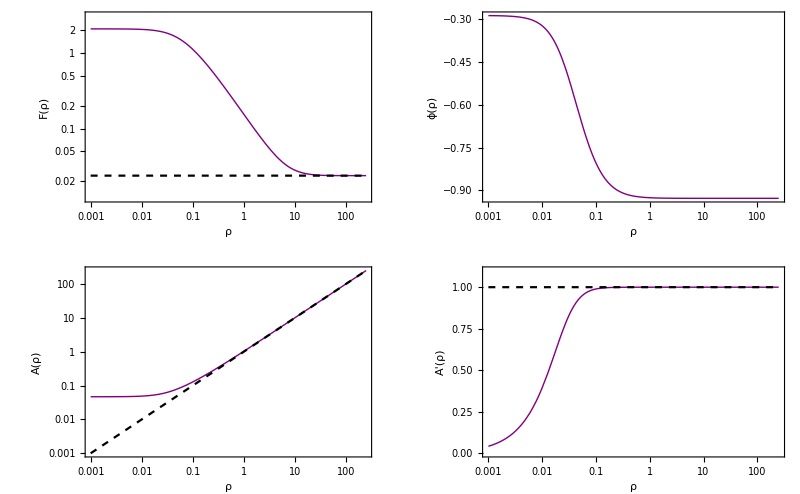

```mathematica
MakePlot[] (* Plot the results *)
```